```mathematica
Clear["Global`*"]
```

# Heat Equation Solution PDE equation (∂u(x, t))/(∂t)=(∂^2 u(x,t))/(∂x^2){u(x,0)=0 |x|≤1/2 u(x,0)=1 |x|>1/2

```mathematica
f[x_]:=x;
```

```mathematica
g[x_]:=If[f[x]<0.5  && f[x] > -0.5,1,0];
```

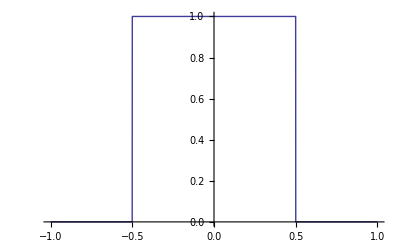

```mathematica
Plot[g[x],{x,-1,1}]
```

```mathematica
sol=NDSolve[{D[u[x,t],t]==D[u[x,t],x,x],u[x,0]==g[x],u[1,t]==0,u[-1,t]==0},u,{x,-1,1},{t,0,1}, MaxStepSize->0.1]
```

NDSolve::mxsst: Using maximum number of grid points 10000 allowed by the MaxPoints or MinStepSize options for independent variable x.

{{u→InterpolatingFunction[{{-1.,1.},{0.,1.}},<>]}}

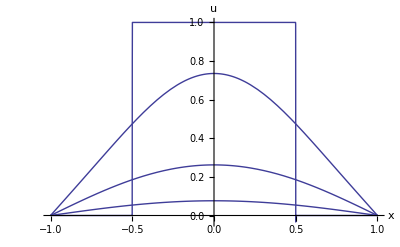

```mathematica
pl=GraphicsGrid[{{Plot3D[Evaluate[u[x,t]/. sol[[1]]], {t,0,1},{x,-1,1}, Mesh->True, AxesLabel->{t,x,u}],Plot[Table[Evaluate[u[x,t]/.sol[[1]]],{t,{0,0.1,0.5,1}}],{x,-1,1}, AxesLabel->{x,u}]}}, Frame->All, ImageSize->{700,350}]
```